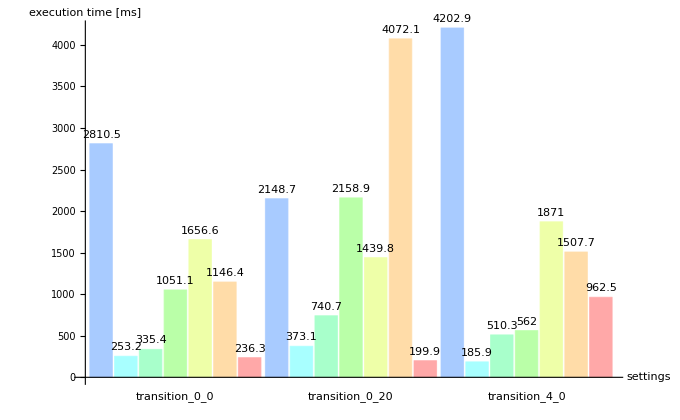
-Graphics--Graphics- | cryptominisat(jni)
-Graphics- | glucose(jni)
-Graphics- | minisat(jni)
-Graphics- | sat4j
-Graphics- | lingeling(jni)
-Graphics- | plingeling(jni)
-Graphics- | minisatprover(jni)

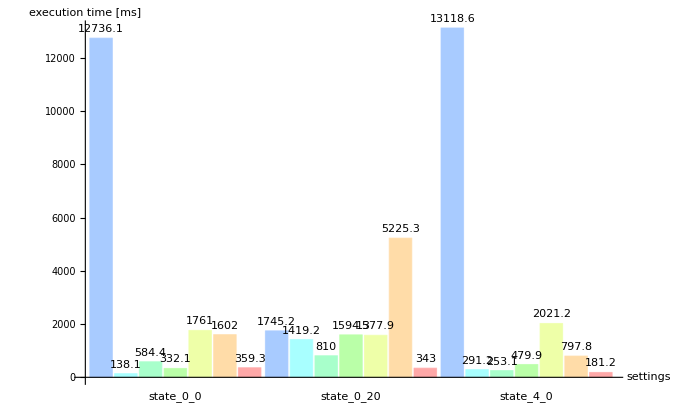
-Graphics--Graphics- | cryptominisat(jni)
-Graphics- | glucose(jni)
-Graphics- | minisat(jni)
-Graphics- | sat4j
-Graphics- | lingeling(jni)
-Graphics- | plingeling(jni)
-Graphics- | minisatprover(jni)

```mathematica
simple=Import["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/simple_alloyoptions_2_aggregated.csv","table",FieldSeparators->";"];
labels1=simple[[2;;4, 1]];
values1=simple[[2;;4,2;;8]];
labels2=simple[[5;;7, 1]];
values2=simple[[5;;7,2;;8]];
legends=simple[[1, 2;;8]];
simple1=BarChart[values1,ChartLabels->{labels1,None}, ChartLegends -> legends,AxesLabel->{"settings","execution time [ms]"},LabelingFunction->(Placed[#,Above]&), ImageSize -> 680]
simple2=BarChart[values2,ChartLabels->{labels2,None}, ChartLegends -> legends,AxesLabel->{"settings","execution time [ms]"}, LabelingFunction->(Placed[#,Above]&), ImageSize -> 680]
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/options_transition.png", simple1];
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/options_state.png", simple2];
```

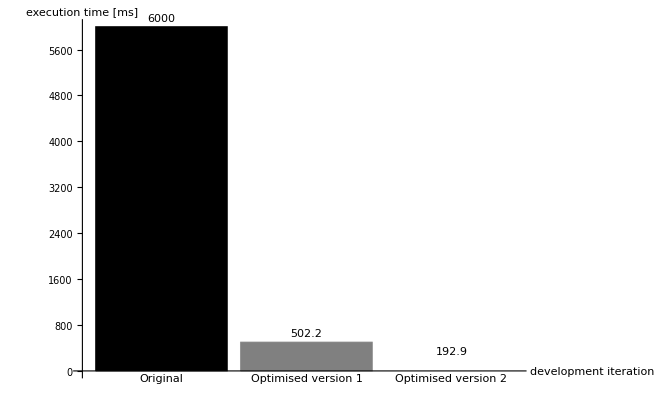

```mathematica
optimalizations=Import["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/optimalizations_aggregated.csv","table",FieldSeparators->";"];
(*values1={};
Do[values1=Append[values1, optimalizations[[2;;3,i]]],{i,2,8}]*)
values2 = {6000,optimalizations[[5,3]],optimalizations[[6,3]]};
labels = {"Original", "Optimised version 1", "Optimised version 2"};
(*optimalization1=BarChart[values1,ChartLabels->{labels,None}, ChartLegends -> legends,AxesLabel->{"SAT solver","execution time [ms]"}, LabelingFunction->(Placed[#,Above]&),ChartStyle -> {Yellow, Black}, ImageSize -> 670]*)
optimalization2=BarChart[values2,ChartLabels->{labels},AxesLabel->{"development iteration","execution time [ms]"}, LabelingFunction->(Placed[#,Above]&),ChartStyle -> {Black, Gray, White}, ImageSize -> 670]
(*Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/optimalization_state.png", optimalization1];*)
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/optimalization_transition.png", optimalization2];
```

```mathematica
0
```

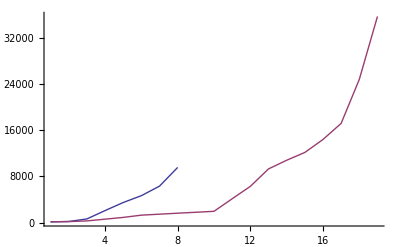

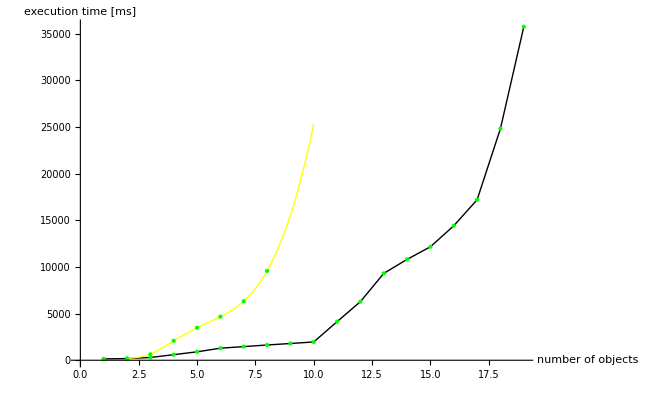

```mathematica
scalabilitystate=Import["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/scalability_state_aggregated2.csv","table",FieldSeparators->";"];
values1=scalabilitystate[[2]];
scalabilitytransition=Import["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/scalability_transition_aggregated2.csv","table",FieldSeparators->";"];
values2=scalabilitytransition[[2]];
legends={"states","transitions"};
ListLinePlot[{values1, values2}, PlotRange -> All]
f1=ListInterpolation[values1];
states=Plot[f1[x],{x,2,10}, PlotStyle -> {Yellow, Thick}];
transitions=ListLinePlot[values2, PlotStyle -> {Black, Thick}];
scalability=Show[transitions, states,ListPlot[{values1, values2},PlotStyle -> {{Green, PointSize[Large]},{Green, PointSize[Large]}}], AxesLabel->{"number of objects","execution time [ms]"}, ImageSize -> 650]
Export["/home/chef/Egyetem/Onlab1/msc-thesis/measurements/scalability.png", scalability];
```